```mathematica
{fM, fV, fu} = {M, V, u} /. DSolve[
{
M[x] == EI u''[x],
V'[x] == -w,
M'[x] == V[x],
u[0] == 0, u'[0] == 0,
u[L] == 0, u'[L] == 0
},
{
M, V, u
},
x
][[1]]
```

{Function[{x},1/12 (-L^2 w+6 L w x-6 w x^2)],Function[{x},1/2 (L w-2 w x)],Function[{x},(-L^2 w x^2+2 L w x^3-w x^4)/(24 EI)]}

```mathematica
fM[L]
```

-(L^2 w)/12

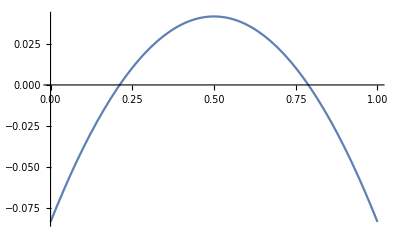

```mathematica
Block[ {w, L, EI},
{w, L, EI} = {1, 1, 1};
Plot[fM[x], {x, 0, L}]
]
```

```mathematica
DSolve[{y'[t]== y[t],y[0] == 1 }, y[t], t]
```

{{y[t]→ⅇ^t}}

```mathematica
(b h^3)/12
```